```mathematica
RemoveFirst [set_,el_]:=Block[{result=set,i},
For[i=1,i<=Length[set],i++,
If[result[[i]]==el,Return[Delete[result,i]]]
];
set
]
```

```mathematica
RemoveFirst[{1,1,2,2,3},2]
```

{1,1,2,3}

```mathematica
SetRemove[big_,small_]:=Block[{result={},todo=small},
Table[
If[MemberQ[todo,el],
todo=RemoveFirst[todo,el]
,
AppendTo[result,el]
]
,{el,big}
];
result
]
```

```mathematica
SetRemove[{1,1,2,2,3},{1,1,2,3}]
```

```mathematica
CommonItems[set1_,set2_]:=Block[{result={},todo=set2},
Table[
If[MemberQ[todo,el],
AppendTo[result,el];
todo=RemoveFirst[todo,el]
]
,{el,set1}
];
result
]
```

```mathematica
CommonItems[{1,1,2,2,3},{1,1,2,3}]
```

{1,1,2,3}

```mathematica
IsTypeRefinement[many_,few_]:=Block[{common,manyleft,fewleft},
If[Length[many]==Length[few]+1,
common= CommonItems[many,few];
manyleft=SetRemove[many,common];
fewleft=SetRemove[few,common];
Length[manyleft]==2&&Length[fewleft]==1&&Total[manyleft]==Total[fewleft]
,
False
]
]
```

```mathematica
IsTypeRefinement[{2,2,1,1,1,1},{2,2,2,1,1}]
```

{2,2,1,1}

True

```mathematica
ReverseGraph
```

```mathematica
PartitionTypeLattice[set_]:=Block[{com=Subsets[set,{2}],result={}},
Table[
If[IsTypeRefinement[pair[[1]],pair[[2]]],
AppendTo[result,DirectedEdge[pair[[1]],pair[[2]]]],
If[IsTypeRefinement[pair[[2]],pair[[1]]],
AppendTo[result,DirectedEdge[pair[[2]],pair[[1]]]]
]
]
,
{pair,com}
];
result
]
```

```mathematica
always8=Calcalways[doc8]
```

{{2,2,2,1,1},{2,2,1,1,1,1},{2,1,1,1,1,1,1},{1,1,1,1,1,1,1,1}}

```mathematica
IsTypeRefinement[{2,2,1,1,1,1},{2,2,2,1,1}]
```

{2,2,1,1,1,1}

False

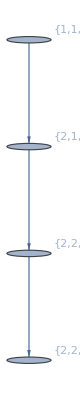

```mathematica
Graph[PartitionTypeLattice[always8],VertexLabels->"Name",GraphLayout->"LayeredDigraphEmbedding"]
```

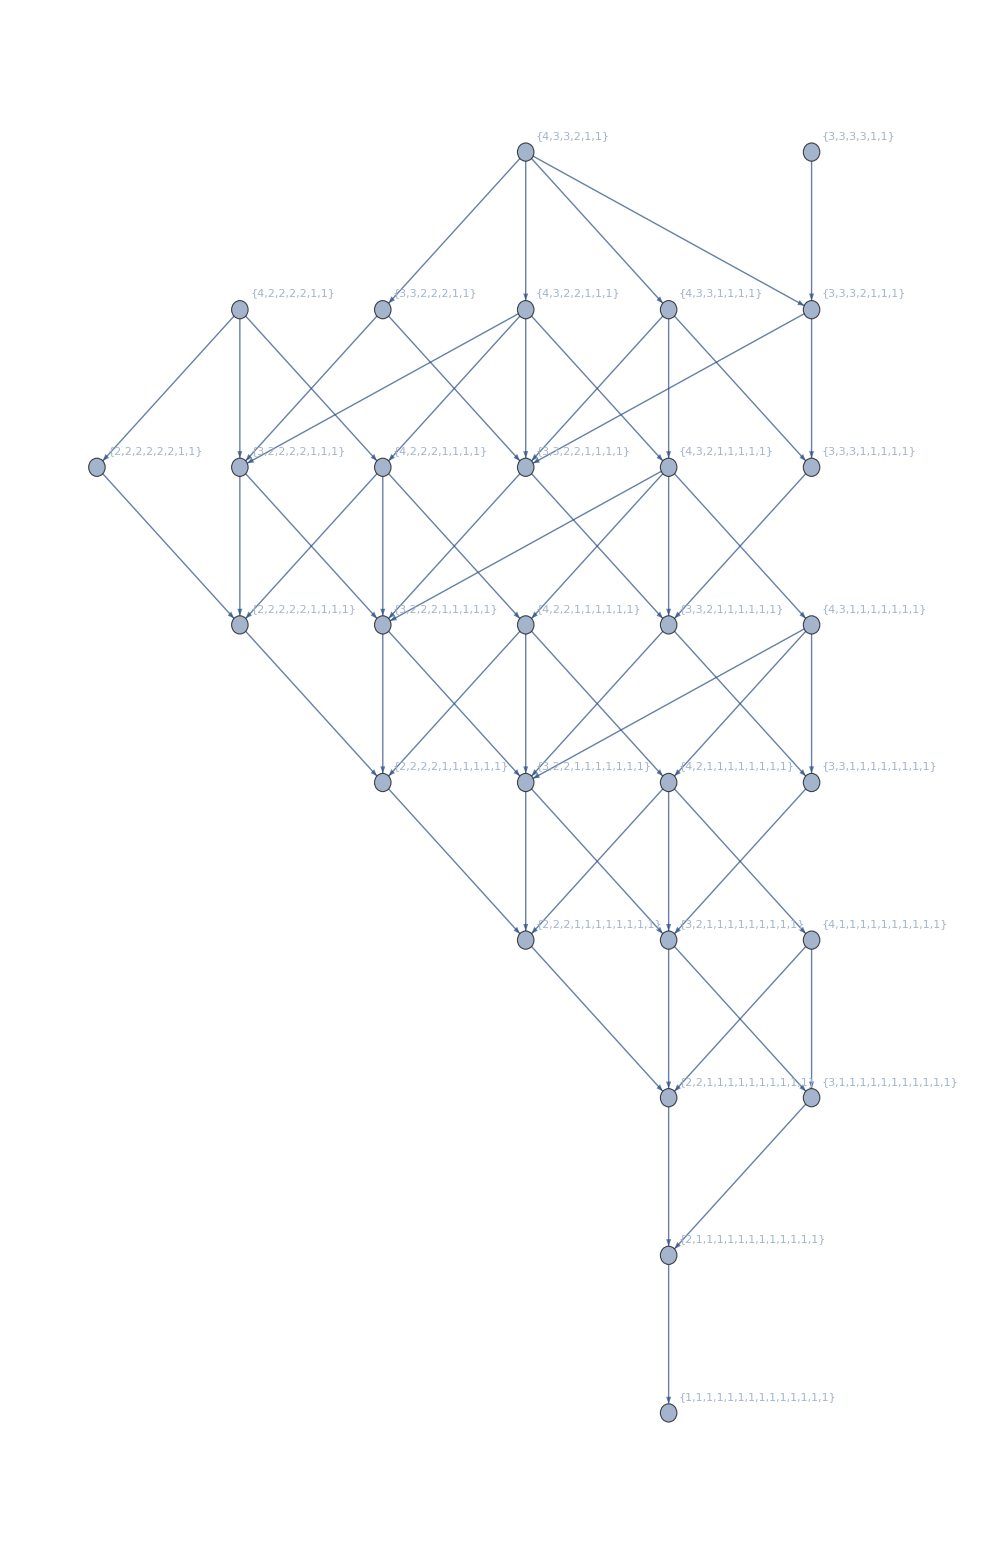

```mathematica
ReverseGraph[Graph[PartitionTypeLattice[Calcalways[doc14]],VertexLabels->"Name",GraphLayout->"LayeredDigraphEmbedding"]]
```

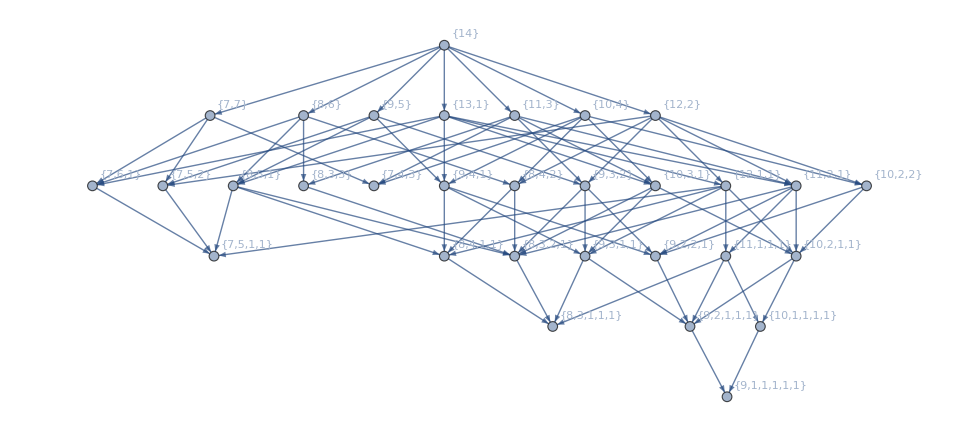

```mathematica
ReverseGraph[Graph[PartitionTypeLattice[CalcNever[doc14]],VertexLabels->"Name",GraphLayout->"LayeredDigraphEmbedding"]]
```

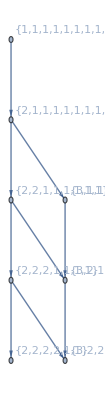

```mathematica
Graph[PartitionTypeLattice[Calcalways[doc10]],VertexLabels->"Name",GraphLayout->"LayeredDigraphEmbedding"]
```

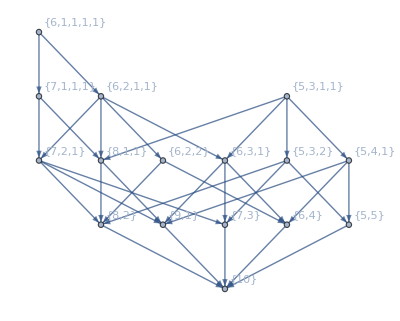

```mathematica
Graph[PartitionTypeLattice[CalcNever[doc10]],VertexLabels->"Name",GraphLayout->"LayeredDigraphEmbedding"]
```

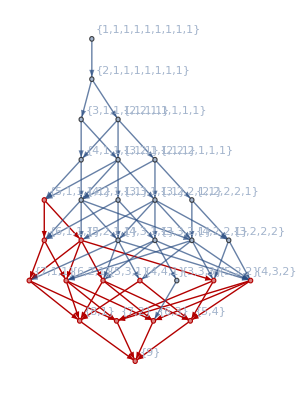

```mathematica
Graph[PartitionTypeLattice[IntegerPartitions[9]],VertexLabels->"Name",GraphLayout->"LayeredDigraphEmbedding", GraphHighlight->With[{ggg=PartitionTypeLattice[CalcNever[doc9]]},
Join[EdgeList[ggg],VertexList[ggg]]], GraphHighlightStyle->"Thick"]
```